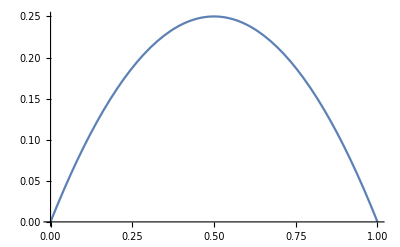

```mathematica
Plot[p*(1-p),{p,0,1}]
```

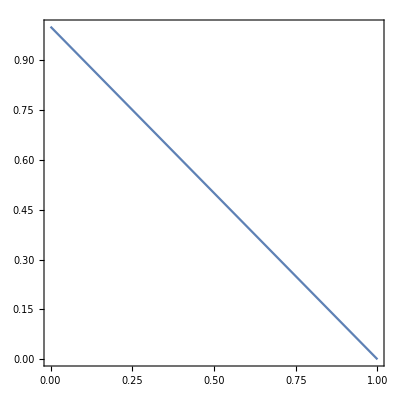

```mathematica
ContourPlot[p+q==1,{p,0,1},{q,0,1}]
```

```mathematica
ContourPlot3D[p1+p2+p3==1,{p1,0,1},{p2,0,1},{p3,0,1}]
```

-Graphics3D-

```mathematica
RegionPlot3D[u<=p q&&p+q==1,{p,0,1},{q,0,1},{u,0,1}]
```

-Graphics3D-

```mathematica
data=Table[{p,(1-p),p (1-p)},{p,0,1,0.01}];
hyperplane=Table[{p,1-p,1/4 p+1/4 (1-p)},{p,0,1,0.01}];
ListPlot3D[{data,hyperplane},Mesh->None,InterpolationOrder->0,ColorFunction->"SouthwestColors",Axes->True]
```

-Graphics3D-

```mathematica
Plot3D[{p q,1/4 p+1/4 q},{p,0,1},{q,0,1},PlotLegends->"Expressions"]
```

-Graphics3D-

```mathematica
Reduce[1/4 p + 1/4 q ≥ p q&&p+q==1, {p, q}]
```

p∈Reals&&q==1-p

```mathematica
ContourPlot3D[{u==1/4 p + 1/4 q,p+q==1}, , {p,0,1},{q,0,1},{u,0,1}]
```

ContourPlot3D::nonopt: Options expected (instead of {u, 0, 1}) beyond position 4 in ContourPlot3D[{u == p/4 + q/4, p + q == 1}, Null, {p, 0, 1}, {q, 0, 1}, {u, 0, 1}]. An option must be a rule or a list of rules.

ContourPlot3D[{u==p/4+q/4,p+q==1},Null,{p,0,1},{q,0,1},{u,0,1}]

```mathematica
ListPlot3D[Table[{p,q,1/4 p + 1/4 q}, {p, 0, 1, 0.01}, {q,0,1,0.01}]]
```

-Graphics3D-

```mathematica
Manipulate[
Plot[{x (1-x),(1-2p)x+p^2},{x,0,1}],
{p,0,1,0.01}
]
```